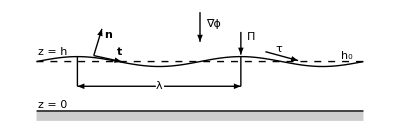

```mathematica
h0=.5;
a=-1;
b=1;
λ=1;
A=0.05;
f[x_]:=A*Sin[(2π/λ) x]+h0
x1=-0.65;
length = 0.17;
Show[Plot[{A*Sin[(2π/λ) x]+h0,0},{x,a,b},PlotRange->{-0.1,1},PlotStyle->{Directive[Black,Thick]},Axes->False,Filling->{2->Bottom}],
Graphics[{Arrowheads[Medium],Arrow[{{0,1},{0,0.7}}],Arrow[{{1/4,.8},{1/4,0.57}}],Arrow[{{.4,.6},{.6,0.51}}],Text[Style["∇ϕ",Medium,Black],{.08,.88}],Text[Style["Π",Medium,Black],{.31,.75}],Text[Style["τ",Medium,Black],{.48,.63}],Text[Style["h_0",Medium,Black],{.9,.56}],Dashed,Line[{{a,h0},{b,h0}}]}],Graphics[{Arrowheads[Medium],Line[{{-3/4,h0+A},{-3/4,h0/2}}],Line[{{1/4,h0+A},{1/4,h0/2}}],Text[Style["λ",Black,Medium],{-1/4,h0/2}],Arrow[{{-.22,h0/2},{1/4,h0/2}}],Arrow[{{-.27,h0/2},{-3/4,h0/2}}],Arrow[{{x1,f[x1]+0.02},{x1+0.05,f[x1]-0.05/f'[x1]+0.02}}],Arrow[{{x1,f[x1]+0.02},{x1+length,f[x1]+length*f'[x1]-0.01}}],Text[Style["n",Black,Bold,Medium],{x1+0.09,f[x1]+0.23}],Text[Style["t",Black,Bold,Medium],{x1+0.16,f[x1]+0.06}],Text[Style["z = 0",Black, Medium],{-.9,0.06}],Text[Style["z = h", Black, Medium],{-.9,h0+.1}]}],AspectRatio->1/3]
```

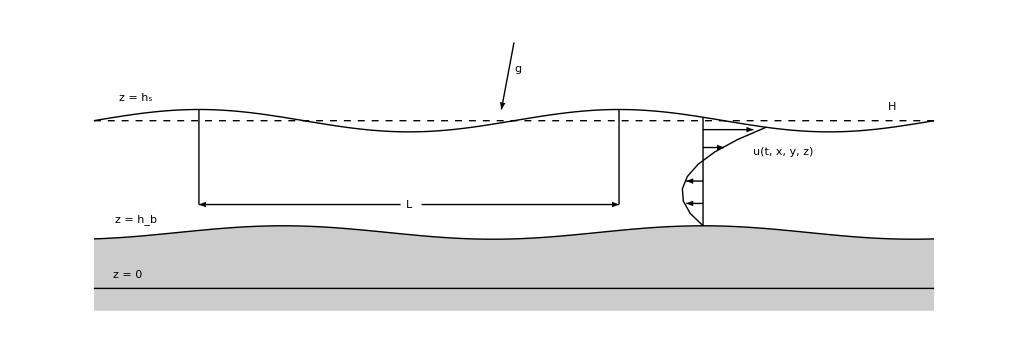

```mathematica
h0=.75;
a=-1;
b=1;
λ=1;
as=0.05;
hsm=0.75;
hs[x_]:=as*Sin[(2π/λ) x]+hsm;
ab=0.03;
hbm=0.25;
xb=0.2;
hb[x_]:=ab*Sin[(2π/λ )(x-xb)]+hbm
h[x_]:=hs[x]-hb[x]
x1=-0.65;
length = 0.17;
Show[Plot[{hs[x],hb[x],0},{x,a,b},PlotRange->{-0.1,1.15},PlotStyle->{Directive[Black,Thick]},Axes->False,Filling->{2->Bottom}],
Graphics[{Arrowheads[Medium],
Arrow[{{0,1.1},{-.03,0.8}}],
Text[Style["g",Medium,Black],{.01,.98}],
Text[Style["H",Medium,Black],{.9,hsm+0.06}],
Dashed,Line[{{a,hsm},{b,hsm}}]}],
Graphics[{Arrowheads[Medium],
Line[{{-3/4,hsm+as},{-3/4,hsm/2}}],
Line[{{1/4,hsm+as},{1/4,hsm/2}}],
Text[Style["L",Black,Medium],{-1/4,hsm/2}],
Arrow[{{-.22,hsm/2},{1/4,hsm/2}}],
Arrow[{{-.27,hsm/2},{-3/4,hsm/2}}],
Text[Style["z = 0",Black, Medium],{-.92,0.06}],
Text[Style["z = h_s", Black, Medium],{-.9,hsm+.1}],
Text[Style["z = h_b", Black, Medium],{-.9,hbm+.06}],
Line[{{0.45, hb[0.45]},{0.45,hs[0.45]}}],
BezierCurve[{{0.45, hb[0.45]},{0.3, 0.5},{0.6, hs[0.6]}}],
Arrowheads[Small],
Arrow[{{0.45, hb[0.45]+0.1},{0.41,hb[0.45]+0.1}}],
Arrow[{{0.45, hb[0.45]+0.2},{0.41,hb[0.45]+0.2}}],
Arrow[{{0.45, hb[0.45]+0.35},{0.5,hb[0.45]+0.35}}],
Arrow[{{0.45, hb[0.45]+0.43},{0.57,hb[0.45]+0.43}}],
Text[Style["u(t, x, y, z)", Black, Medium],{0.64,hb[0.45]+ 0.33}]
}],
AspectRatio->1/3]
```

```mathematica
.
```

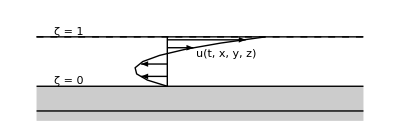

```mathematica
h0=.75;
a=0.25;
b=0.75;
λ=1;
as=0.05;
hsm=0.75;
hs[x_]:=hsm;
ab=0.03;
hbm=0.25;
xb=0.2;
hb[x_]:=hbm
h[x_]:=hs[x]-hb[x]
x1=-0.65;
length = 0.17;
Show[Plot[{hsm,hbm,0},{x,a,b},PlotRange->{-0.1,1},PlotStyle->{Directive[Black,Thick]},Axes->False,Filling->{2->Bottom}],
Graphics[{Arrowheads[Medium],
Dashed,Line[{{a,hsm},{b,hsm}}]}],
Graphics[{Arrowheads[Medium],
Text[Style["ζ = 1", Black, Medium],{a+0.05,hsm+0.05}],
Text[Style["ζ = 0", Black, Medium],{a+0.05,hbm+0.05}],
Line[{{0.45, hb[0.45]},{0.45,hs[0.45]}}],
BezierCurve[{{0.45, hb[0.45]},{0.3, 0.5},{0.6, hs[0.6]}}],
Arrowheads[Small],
Arrow[{{0.45, hb[0.45]+0.1},{0.41,hb[0.45]+0.1}}],
Arrow[{{0.45, hb[0.45]+0.225},{0.41,hb[0.45]+0.225}}],
Arrow[{{0.45, hb[0.45]+0.39},{0.49,hb[0.45]+0.39}}],
Arrow[{{0.45, hb[0.45]+0.47},{0.57,hb[0.45]+0.47}}],
Text[Style["u(t, x, y, z)", Black, Medium],{0.54,hb[0.45]+ 0.33}]
}],
AspectRatio->1/3]
```

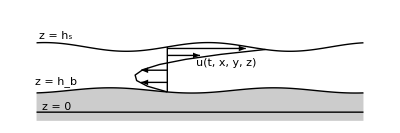

```mathematica
h0=.75;
a=0.25;
b=0.75;
λ=1/4;
as=0.05;
hsm=0.75;
hs[x_]:=as*Sin[(2π/λ)( x-0.2)]+hsm;
ab=0.03;
hbm=0.25;
xb=-.2;
hb[x_]:=ab*Sin[(2π/λ )(x-xb)]+hbm
h[x_]:=hs[x]-hb[x]
x1=-0.65;
length = 0.17;
Show[Plot[{hs[x],hb[x],0},{x,a,b},PlotRange->{-0.1,1.15},PlotStyle->{Directive[Black,Thick]},Axes->False,Filling->{2->Bottom}],
Graphics[{Arrowheads[Medium],
Text[Style["z = 0",Black, Medium],{a+0.03,0.06}],
Text[Style["z = h_s", Black, Medium],{a+0.03,hsm+.12}],
Text[Style["z = h_b", Black, Medium],{a+0.03,hbm+.1}],
Line[{{0.45, hb[0.45]},{0.45,hs[0.45]}}],
BezierCurve[{{0.45, hb[0.45]},{0.3, 0.5},{0.6, hs[0.6]}}],
Arrowheads[Small],
Arrow[{{0.45, hb[0.45]+0.11},{0.41,hb[0.45]+0.11}}],
Arrow[{{0.45, hb[0.45]+0.25},{0.41,hb[0.45]+0.25}}],
Arrow[{{0.45, hb[0.45]+0.42},{0.5,hb[0.45]+0.42}}],
Arrow[{{0.45, hb[0.45]+0.5},{0.57,hb[0.45]+0.5}}],
Text[Style["u(t, x, y, z)", Black, Medium],{0.54,hb[0.45]+ 0.33}]
}],
AspectRatio->1/3]
```